## 1 - Amostragem

θ = parâmetro, o valor real da característica na população. μ (média), σ^2 (variância) e ρ (coeficiente de correlação) são parâmetros.

θ̂ = estimador, estatística de parâmetro. Função dos elementos da amostra. É uma variável aleatória (pois os valores são diferentes em cada amostra). x̄ (média), s^2 (variância) e r (coeficiente de correlação) são estimadores.

(θ̂)_0 = estimativa, o valor obtido pelo estimador.

ϵ = θ-θ̂, o erro amostral. Soma da parte casual com a parte viés/desvio, em que casual é a diferença entre a estimativa e a esperança do estimador (θ̂-E(θ̂)); e viés é a esperança menos o parâmetro na população (E(θ̂)-θ).

Como o erro casual é natural, se tira que sempre há uma esperança diferente da estimativa. O viés é a esperança não estar alinhada ao parâmetro, mas se supõe que isto possa ser eliminado.

E(θ̂) = ”esperança matemática” da variável aleatória.

Viés de seleção: algum elemento ter chance de não pertencer a uma amostra (“eliminação”). Se houver alguma chance para todos os elementos (probabilística), não há viés de seleção.

“The expected value of a random variable, intuitively, is the long-run average value of repetitions of the same experiment it represents. (...) For example, the expected value in rolling a six-sided die is 3.5, because the average of all the numbers that come up is 3.5 as the number of rolls approaches infinity. In other words, the law of large numbers states that the arithmetic mean of the values almost surely converges to the expected value as the number of repetitions approaches infinity. (...) More practically, the expected value of a discrete random variable is the probability-weighted average of all possible values. In other words, each possible value the random variable can assume is multiplied by its probability of occurring, and the resulting products are summed to produce the expected value. The same principle applies to an absolutely continuous random variable, except that an integral of the variable with respect to its probability density replaces the sum. (...) The expected value is a key aspect of how one characterizes a probability distribution; it is one type of location parameter. By contrast, the variance is a measure of dispersion of the possible values of the random variable around the expected value. The variance itself is defined in terms of two expectations: it is the expected value of the squared deviation of the variable’s value from the variable’s expected value.”1

“Let X be a random variable with a finite number of finite outcomes x_1, x_2, ..., x_k occurring with probabilities p_1, p_2, ...,  p_k. The expectation of x is defined as E(X)=∑_(i=1)^k x_i p_i. Since all probabilities add up to 1, the expected value is the weighted average, with the probabilities being the weights.”

“The weighted arithmetic mean is similar to an ordinary arithmetic mean (the most common type of average), except that instead of each of the data points contributing equally to the final average, some data points contribute more than others. If all the weights are equal, then the weighted mean is the same as the arithmetic mean.”2

If all outcomes are equiprobable, then the weighted average turns into the simple average. This is intuitive: the expected value of a random variable is the average of all values it can take; thus the expected value is what one expects to happen on average.
If the outcomes are not equiprobable, then the simple average must be replaced with the weighted average, which takes into account the fact that some outcomes are more likely than the others. The intuition however remains the same: the expected value of X is what one expects to happen on average.”3

Ou seja, estamos lidando com a distribuição da variável aleatória.
O que significa a distribuição dos valores que ela gera em cada execução, o que é um valor para cada amostra.

## 2 - Análise exploratória dos dados de uma amostra

Não conheçamos a média e variância de uma população X. Retiramos uma amostra de n elementos e estimamos estes parâmetros.

Estimador média x̄=(∑_(i=1)^n x_i)/n, estimador variância s^2=(∑_(i=1)^n (x_i-x̄)^2)/(n-1).

Estimador média não viciado/enviesado pois E(x̄)=μ. (A esperança da média amostral é igual à média populacional.)
Estimador variância não viciado/enviesado pois E(s^2)=σ^2. (A esperança da variância amostral é igual à variância populacional.)

O estimador de variância s^2=(∑_(i=1)^n (x_i-x̄)^2)/n é viciado/enviesado: E(s^2)≠σ^2. (A esperança da variância amostral é diferente da variância populacional.)

```mathematica
Clear[log]
log=SemanticImport[
	NotebookDirectory[]<>"LogTest1.txt",
	<|"PIM"->Automatic|>,
	"NamedColumns",HeaderLines->1,Delimiters->";"];
```

```mathematica
Length[log["PIM"]]
```

29225

```mathematica
N[{(∑_(i=1)^Length[log["PIM"]] log["PIM"][[i]])/Length[log["PIM"]],Mean[log["PIM"]]}]
```

{3195.73,3195.73}

```mathematica
N[{(∑_(i=1)^Length[log["PIM"]] (log["PIM"][[i]]-Mean[log["PIM"]])^2)/(Length[log["PIM"]]-1),Variance[log["PIM"]]}]
```

{2.27091×10^7,2.27091×10^7}

```mathematica
N[(∑_(i=1)^Length[log["PIM"]] (log["PIM"][[i]]-Mean[log["PIM"]])^2)/Length[log["PIM"]]]
```

2.27084×10^7

Viciado valor um pouco diferente.

```mathematica
Clear[data1]
data1={5,9,2,8.8,6.3,10.1,3.4,2.9,4.1};
```

Se o viés é a esperança ser diferente do parâmetro, a esperança vem da própria amostra (e não da população). O cálculo da esperança é a multiplicação... temos algumas variáveis diferentes:

A média da amostra

O valor dos elementos

A probabilidade dos elementos

Apenas algumas amostras.

```mathematica
Module[{samples,means},
Print[Mean[data1]];
Print[samples=Table[Flatten[Subsets[RandomSample[data1],{3},1]],3]];
Print[means=Table[N[Mean[sample]],{sample,samples}]];
Print[Mean[means]];
]
```

5.73333

{{4.1,6.3,5},{5,3.4,2.9},{10.1,4.1,3.4}}

{5.13333,3.76667,5.86667}

4.92222

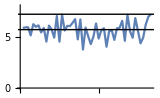
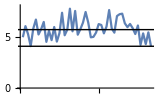
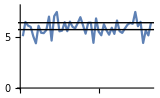
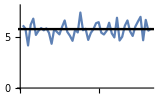
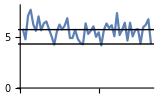
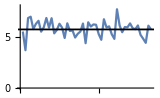

```mathematica
Module[{samples,means,meansMean},
Table[
meansMean=Table[
samples=Table[Flatten[Subsets[RandomSample[data1],{3},1]],3];
means=Table[N[Mean[sample]],{sample,samples}];
Mean[means]
,50];
ListLinePlot[meansMean,ImageSize->160,PlotRange->{0,8},Epilog->{,{InfiniteLine[{{0,Mean[data1]},{2,Mean[data1]}}],InfiniteLine[{{0,Mean[means]},{2,Mean[means]}}]}}]
,6]
]
```

Média das médias diferente, mas sempre variando em uma faixa.

Todas as amostras.

5.73333

{{8.8,4.1,6.3},{8.8,4.1,2.9},{8.8,4.1,2},{8.8,4.1,3.4},{8.8,4.1,10.1},{8.8,4.1,5},{8.8,4.1,9},{8.8,6.3,2.9},{8.8,6.3,2},{8.8,6.3,3.4},{8.8,6.3,10.1},{8.8,6.3,5},{8.8,6.3,9},{8.8,2.9,2},{8.8,2.9,3.4},{8.8,2.9,10.1},{8.8,2.9,5},{8.8,2.9,9},{8.8,2,3.4},{8.8,2,10.1},{8.8,2,5},{8.8,2,9},{8.8,3.4,10.1},{8.8,3.4,5},{8.8,3.4,9},{8.8,10.1,5},{8.8,10.1,9},{8.8,5,9},{4.1,6.3,2.9},{4.1,6.3,2},{4.1,6.3,3.4},{4.1,6.3,10.1},{4.1,6.3,5},{4.1,6.3,9},{4.1,2.9,2},{4.1,2.9,3.4},{4.1,2.9,10.1},{4.1,2.9,5},{4.1,2.9,9},{4.1,2,3.4},{4.1,2,10.1},{4.1,2,5},{4.1,2,9},{4.1,3.4,10.1},{4.1,3.4,5},{4.1,3.4,9},{4.1,10.1,5},{4.1,10.1,9},{4.1,5,9},{6.3,2.9,2},{6.3,2.9,3.4},{6.3,2.9,10.1},{6.3,2.9,5},{6.3,2.9,9},{6.3,2,3.4},{6.3,2,10.1},{6.3,2,5},{6.3,2,9},{6.3,3.4,10.1},{6.3,3.4,5},{6.3,3.4,9},{6.3,10.1,5},{6.3,10.1,9},{6.3,5,9},{2.9,2,3.4},{2.9,2,10.1},{2.9,2,5},{2.9,2,9},{2.9,3.4,10.1},{2.9,3.4,5},{2.9,3.4,9},{2.9,10.1,5},{2.9,10.1,9},{2.9,5,9},{2,3.4,10.1},{2,3.4,5},{2,3.4,9},{2,10.1,5},{2,10.1,9},{2,5,9},{3.4,10.1,5},{3.4,10.1,9},{3.4,5,9},{10.1,5,9}}

{6.4,5.26667,4.96667,5.43333,7.66667,5.96667,7.3,6.,5.7,6.16667,8.4,6.7,8.03333,4.56667,5.03333,7.26667,5.56667,6.9,4.73333,6.96667,5.26667,6.6,7.43333,5.73333,7.06667,7.96667,9.3,7.6,4.43333,4.13333,4.6,6.83333,5.13333,6.46667,3.,3.46667,5.7,4.,5.33333,3.16667,5.4,3.7,5.03333,5.86667,4.16667,5.5,6.4,7.73333,6.03333,3.73333,4.2,6.43333,4.73333,6.06667,3.9,6.13333,4.43333,5.76667,6.6,4.9,6.23333,7.13333,8.46667,6.76667,2.76667,5.,3.3,4.63333,5.46667,3.76667,5.1,6.,7.33333,5.63333,5.16667,3.46667,4.8,5.7,7.03333,5.33333,6.16667,7.5,5.8,8.03333}

5.73333

5.73333

{{9,4.1,8.8},{9,4.1,5},{9,4.1,2.9},{9,4.1,6.3},{9,4.1,10.1},{9,4.1,3.4},{9,4.1,2},{9,8.8,5},{9,8.8,2.9},{9,8.8,6.3},{9,8.8,10.1},{9,8.8,3.4},{9,8.8,2},{9,5,2.9},{9,5,6.3},{9,5,10.1},{9,5,3.4},{9,5,2},{9,2.9,6.3},{9,2.9,10.1},{9,2.9,3.4},{9,2.9,2},{9,6.3,10.1},{9,6.3,3.4},{9,6.3,2},{9,10.1,3.4},{9,10.1,2},{9,3.4,2},{4.1,8.8,5},{4.1,8.8,2.9},{4.1,8.8,6.3},{4.1,8.8,10.1},{4.1,8.8,3.4},{4.1,8.8,2},{4.1,5,2.9},{4.1,5,6.3},{4.1,5,10.1},{4.1,5,3.4},{4.1,5,2},{4.1,2.9,6.3},{4.1,2.9,10.1},{4.1,2.9,3.4},{4.1,2.9,2},{4.1,6.3,10.1},{4.1,6.3,3.4},{4.1,6.3,2},{4.1,10.1,3.4},{4.1,10.1,2},{4.1,3.4,2},{8.8,5,2.9},{8.8,5,6.3},{8.8,5,10.1},{8.8,5,3.4},{8.8,5,2},{8.8,2.9,6.3},{8.8,2.9,10.1},{8.8,2.9,3.4},{8.8,2.9,2},{8.8,6.3,10.1},{8.8,6.3,3.4},{8.8,6.3,2},{8.8,10.1,3.4},{8.8,10.1,2},{8.8,3.4,2},{5,2.9,6.3},{5,2.9,10.1},{5,2.9,3.4},{5,2.9,2},{5,6.3,10.1},{5,6.3,3.4},{5,6.3,2},{5,10.1,3.4},{5,10.1,2},{5,3.4,2},{2.9,6.3,10.1},{2.9,6.3,3.4},{2.9,6.3,2},{2.9,10.1,3.4},{2.9,10.1,2},{2.9,3.4,2},{6.3,10.1,3.4},{6.3,10.1,2},{6.3,3.4,2},{10.1,3.4,2}}

{7.3,6.03333,5.33333,6.46667,7.73333,5.5,5.03333,7.6,6.9,8.03333,9.3,7.06667,6.6,5.63333,6.76667,8.03333,5.8,5.33333,6.06667,7.33333,5.1,4.63333,8.46667,6.23333,5.76667,7.5,7.03333,4.8,5.96667,5.26667,6.4,7.66667,5.43333,4.96667,4.,5.13333,6.4,4.16667,3.7,4.43333,5.7,3.46667,3.,6.83333,4.6,4.13333,5.86667,5.4,3.16667,5.56667,6.7,7.96667,5.73333,5.26667,6.,7.26667,5.03333,4.56667,8.4,6.16667,5.7,7.43333,6.96667,4.73333,4.73333,6.,3.76667,3.3,7.13333,4.9,4.43333,6.16667,5.7,3.46667,6.43333,4.2,3.73333,5.46667,5.,2.76667,6.6,6.13333,3.9,5.16667}

5.73333

5.73333

{{3.4,2.9,8.8},{3.4,2.9,2},{3.4,2.9,9},{3.4,2.9,6.3},{3.4,2.9,10.1},{3.4,2.9,4.1},{3.4,2.9,5},{3.4,8.8,2},{3.4,8.8,9},{3.4,8.8,6.3},{3.4,8.8,10.1},{3.4,8.8,4.1},{3.4,8.8,5},{3.4,2,9},{3.4,2,6.3},{3.4,2,10.1},{3.4,2,4.1},{3.4,2,5},{3.4,9,6.3},{3.4,9,10.1},{3.4,9,4.1},{3.4,9,5},{3.4,6.3,10.1},{3.4,6.3,4.1},{3.4,6.3,5},{3.4,10.1,4.1},{3.4,10.1,5},{3.4,4.1,5},{2.9,8.8,2},{2.9,8.8,9},{2.9,8.8,6.3},{2.9,8.8,10.1},{2.9,8.8,4.1},{2.9,8.8,5},{2.9,2,9},{2.9,2,6.3},{2.9,2,10.1},{2.9,2,4.1},{2.9,2,5},{2.9,9,6.3},{2.9,9,10.1},{2.9,9,4.1},{2.9,9,5},{2.9,6.3,10.1},{2.9,6.3,4.1},{2.9,6.3,5},{2.9,10.1,4.1},{2.9,10.1,5},{2.9,4.1,5},{8.8,2,9},{8.8,2,6.3},{8.8,2,10.1},{8.8,2,4.1},{8.8,2,5},{8.8,9,6.3},{8.8,9,10.1},{8.8,9,4.1},{8.8,9,5},{8.8,6.3,10.1},{8.8,6.3,4.1},{8.8,6.3,5},{8.8,10.1,4.1},{8.8,10.1,5},{8.8,4.1,5},{2,9,6.3},{2,9,10.1},{2,9,4.1},{2,9,5},{2,6.3,10.1},{2,6.3,4.1},{2,6.3,5},{2,10.1,4.1},{2,10.1,5},{2,4.1,5},{9,6.3,10.1},{9,6.3,4.1},{9,6.3,5},{9,10.1,4.1},{9,10.1,5},{9,4.1,5},{6.3,10.1,4.1},{6.3,10.1,5},{6.3,4.1,5},{10.1,4.1,5}}

{5.03333,2.76667,5.1,4.2,5.46667,3.46667,3.76667,4.73333,7.06667,6.16667,7.43333,5.43333,5.73333,4.8,3.9,5.16667,3.16667,3.46667,6.23333,7.5,5.5,5.8,6.6,4.6,4.9,5.86667,6.16667,4.16667,4.56667,6.9,6.,7.26667,5.26667,5.56667,4.63333,3.73333,5.,3.,3.3,6.06667,7.33333,5.33333,5.63333,6.43333,4.43333,4.73333,5.7,6.,4.,6.6,5.7,6.96667,4.96667,5.26667,8.03333,9.3,7.3,7.6,8.4,6.4,6.7,7.66667,7.96667,5.96667,5.76667,7.03333,5.03333,5.33333,6.13333,4.13333,4.43333,5.4,5.7,3.7,8.46667,6.46667,6.76667,7.73333,8.03333,6.03333,6.83333,7.13333,5.13333,6.4}

5.73333

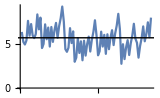
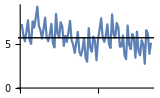
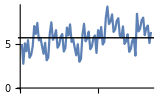

```mathematica
Module[{samples,means},
Table[
Print[Mean[data1]];
Print[samples=Subsets[RandomSample[data1],{3}]];
Print[means=Table[N[Mean[sample]],{sample,samples}]];
Print[Mean[means]];
ListLinePlot[means,Epilog->{,InfiniteLine[{{0,Mean[data1]},{2,Mean[data1]}}]},ImageSize->160]
,3]
]
```

As diferentes linhas só refletem as diferentes ordens das amostras. A média das médias das amostras entre TODAS as amostras  de um tamanho é igual à média da população.

"The expectation value of a function f(x) in a variable x is denoted ⟨f(x)⟩ or E{f(x)}. For a single discrete variable, it is defined by ⟨f(x)⟩=∑_x f(x)P(x), where P(x) is the probability density function. For a single continuous variable it is defined by ⟨f(x)⟩=∫f(x)P(x)ⅆx.”4

Weighted average.

```mathematica
{data1,Length[data1]}
```

{{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1},9}

```mathematica
{∑_(i=1)^Length[data1] data1[[i]],∑_(i=1)^Length[data1] data1[[i]]*(1/Length[data1])}
```

{51.6,5.73333}

A média é a soma dos valores cada um multiplicado por seu “peso”.
Normalmente, o peso é 1/n igual para todos.
Quando há pesos diferentes de 1/n, a média muda.

{0.925717,0.42153,0.599126,0.162005,0.661544,0.154666,0.54544,0.125829,0.0479606}

{0.476347,0.430149,0.53026,0.491552,0.261898,0.800494,0.934369,0.920018,0.315329}

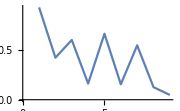
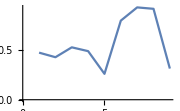

```mathematica
Clear[data1Weights,data1Weights2]
data1Weights=Table[RandomReal[],Length[data1]]
data1Weights2=Table[RandomReal[],Length[data1]]
{ListLinePlot[data1Weights,ImageSize->Small],ListLinePlot[data1Weights2,ImageSize->Small]}
```

```mathematica
{Total[data1Weights],Total[data1Weights2]}
```

{4.77995,3.46624}

```mathematica
{∑_(i=1)^Length[data1] data1[[i]]*data1Weights[[i]],∑_(i=1)^Length[data1] data1[[i]]*data1Weights2[[i]]}
```

{27.8658,18.116}

E se for a soma dos pesos dividida pelos pesos?

```mathematica
{∑_(i=1)^Length[data1] data1[[i]]*(Total[data1Weights]/data1Weights[[i]]),∑_(i=1)^Length[data1] data1[[i]]*(Total[data1Weights]/data1Weights2[[i]])}
```

{632.608,1430.01}

Nada a ver, porque a média aritmética é a soma dos valores multiplicados pelos seus pesos (que no caso de peso uniforme pode ser calculado como 1/n); igualmente a média ponderada é a soma dos valores multiplicados pelos seus pesos, que por não serem uniformes não podem ser calculados, e são informados.

A expectativa da variável randômica é a média ponderada dos valores com as probabilidades como pesos.

Então com cada distribuição de probabilidades diferente, a expectativa é diferente.
Como a expectativa é uma função da distribuição, o objetivo (para alinhar ao parâmetro) é encontrar a mesma distribuição da variável na população.

A diferença da média ponderada para a esperança é que os pesos da média ponderada não somam 1.
Vamos criar um pesos como uma distribuição.

```mathematica
data1
Table[RandomVariate[EmpiricalDistribution[data1]],30]
Mean[EmpiricalDistribution[data1]]
Table[RandomVariate[EmpiricalDistribution[data1Weights->data1]],30]
Mean[EmpiricalDistribution[data1Weights->data1]]
```

{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1}

{6.3,10.1,10.1,3.4,2,8.8,10.1,4.1,6.3,10.1,3.4,9,2,4.1,4.1,2.9,8.8,4.1,9,10.1,2.9,9,10.1,2.9,3.4,6.3,4.1,6.3,6.3,2}

5.73333

{6.3,3.4,3.4,6.3,2,9,9,2.9,2,9,4.1,10.1,10.1,9,5,3.4,9,3.4,3.4,10.1,2,5,9,9,9,3.4,10.1,2,8.8,2.9}

5.82973

Parece que os pesos foram divididos para somar 1.

```mathematica
data1Weights
data1Weights/Total[data1Weights]
Total[data1Weights/Total[data1Weights]]
```

{0.312963,0.629985,0.622442,0.188865,0.765437,0.789048,0.84873,0.42102,0.201459}

{0.0654742,0.131797,0.130219,0.0395118,0.160135,0.165075,0.177561,0.0880805,0.0421467}

1.

Neste caso, a média ponderada seria

```mathematica
∑_(i=1)^Length[data1] data1[[i]]*(data1Weights[[i]]/Total[data1Weights])
```

5.82973

Exatamente.
Que deveria ser a expectativa.

```mathematica
Expectation[x,x\[Distributed]EmpiricalDistribution[data1Weights->data1]]
```

5.82973

Exato.
Então a média aritmética é só a expectativa de um conjunto equiprovável.
E então sempre que se fala na esperança, é apenas a média ponderada sobre as probabilidades que somam 1.

Primeiro verificamos que a média das médias de todas as amostras (ou a expectativa do estimador da média) é igual à média da população, ou seja, o parâmetro.
Agora verificar se o mesmo ocorre para a variância. Agora, a esperança da variância não é a variância das variâncias das amostras, é a média (ponderada sobre as probabilidades?) das variâncias das amostras.

```mathematica
(∑_(i=1)^Length[data1] data1[[i]]-Mean[data1])/(Length[data1]-1)
```

5.73333

Tomando novamente só algumas e todas as amostras.

```mathematica
Module[{samples,variances},
Print["Alguns:"];
Print[samples=Table[RandomSample[data1,3],3]];
Print[variances=N[Table[(∑_(i=1)^Length[sample] sample[[i]]-Mean[sample])/(Length[sample]-1),{sample,samples}]]];
Print["Média aritmética das variâncias:"];
Print[Mean[variances]];
Print["Todos:"];
Print[samples=Subsets[RandomSample[data1],{3}]];
Print[variances=N[Table[(∑_(i=1)^Length[sample] sample[[i]]-Mean[sample])/(Length[sample]-1),{sample,samples}]]];
Print["Média aritmética das variâncias:"];
Print[Mean[variances]];
];
```

Alguns:

{{9,8.8,3.4},{2,9,5},{10.1,6.3,3.4}}

{7.06667,5.33333,6.6}

Média aritmética das variâncias:

6.33333

Todos:

{{3.4,6.3,2},{3.4,6.3,2.9},{3.4,6.3,8.8},{3.4,6.3,10.1},{3.4,6.3,4.1},{3.4,6.3,9},{3.4,6.3,5},{3.4,2,2.9},{3.4,2,8.8},{3.4,2,10.1},{3.4,2,4.1},{3.4,2,9},{3.4,2,5},{3.4,2.9,8.8},{3.4,2.9,10.1},{3.4,2.9,4.1},{3.4,2.9,9},{3.4,2.9,5},{3.4,8.8,10.1},{3.4,8.8,4.1},{3.4,8.8,9},{3.4,8.8,5},{3.4,10.1,4.1},{3.4,10.1,9},{3.4,10.1,5},{3.4,4.1,9},{3.4,4.1,5},{3.4,9,5},{6.3,2,2.9},{6.3,2,8.8},{6.3,2,10.1},{6.3,2,4.1},{6.3,2,9},{6.3,2,5},{6.3,2.9,8.8},{6.3,2.9,10.1},{6.3,2.9,4.1},{6.3,2.9,9},{6.3,2.9,5},{6.3,8.8,10.1},{6.3,8.8,4.1},{6.3,8.8,9},{6.3,8.8,5},{6.3,10.1,4.1},{6.3,10.1,9},{6.3,10.1,5},{6.3,4.1,9},{6.3,4.1,5},{6.3,9,5},{2,2.9,8.8},{2,2.9,10.1},{2,2.9,4.1},{2,2.9,9},{2,2.9,5},{2,8.8,10.1},{2,8.8,4.1},{2,8.8,9},{2,8.8,5},{2,10.1,4.1},{2,10.1,9},{2,10.1,5},{2,4.1,9},{2,4.1,5},{2,9,5},{2.9,8.8,10.1},{2.9,8.8,4.1},{2.9,8.8,9},{2.9,8.8,5},{2.9,10.1,4.1},{2.9,10.1,9},{2.9,10.1,5},{2.9,4.1,9},{2.9,4.1,5},{2.9,9,5},{8.8,10.1,4.1},{8.8,10.1,9},{8.8,10.1,5},{8.8,4.1,9},{8.8,4.1,5},{8.8,9,5},{10.1,4.1,9},{10.1,4.1,5},{10.1,9,5},{4.1,9,5}}

{3.9,4.2,6.16667,6.6,4.6,6.23333,4.9,2.76667,4.73333,5.16667,3.16667,4.8,3.46667,5.03333,5.46667,3.46667,5.1,3.76667,7.43333,5.43333,7.06667,5.73333,5.86667,7.5,6.16667,5.5,4.16667,5.8,3.73333,5.7,6.13333,4.13333,5.76667,4.43333,6.,6.43333,4.43333,6.06667,4.73333,8.4,6.4,8.03333,6.7,6.83333,8.46667,7.13333,6.46667,5.13333,6.76667,4.56667,5.,3.,4.63333,3.3,6.96667,4.96667,6.6,5.26667,5.4,7.03333,5.7,5.03333,3.7,5.33333,7.26667,5.26667,6.9,5.56667,5.7,7.33333,6.,5.33333,4.,5.63333,7.66667,9.3,7.96667,7.3,5.96667,7.6,7.73333,6.4,8.03333,6.03333}

Média aritmética das variâncias:

5.73333

Que bate com a variância da população. Mas a probabilidade não entra no estimador da variância?

Do início. Cada lista de números tem uma média ponderada, que é a soma cada número × seu peso ou ∑_(i=1)^n x_i·p_i. Se a soma dos pesos não for 1, a média ponderada, mesmo de pesos 1, será ≠ da média aritmética. Então vamos descartar estes casos. Se a soma dos pesos for 1, eles podem ser igualitários ou não. Se forem, a p de cada x será 1/n e a média ponderada, agora podendo chamar de esperança, ∑_(i=1)^n x_i/n, que é a fórmula da média aritmética, que é a esperança de números sem peso.

Melhor. Cada lista de números tem uma média ponderada. A média ponderada é um número qualquer, porque os pesos podem ser quaisquer. No caso especial dos pesos serem iguais e 1, a média ponderada reduz a ∑_(i=1)^n x_i·1/n=∑_(i=1)^n x_i/n=(∑_(i=1)^n x_i)/n, que é a média aritmética. Mas este é um caso especial, devemos esquecer média aritmética e pensar em ponderada (multiplicação e não divisão).
Quando os pesos são probabilidades (esperança), a soma é 1. Por isso, cada x_i·p_i será < x_i porque p_i<1.

Todo conjunto X tem pesos, uma média ponderada e variância.

Um passo é estabelecer quais são os pesos para cada elemento.
Ao se fazer, obtém-se a distribuição e média ponderada do conjunto.
A variância também depende dos pesos (indiretamente) porque ela é a diferença para a média ponderada:

Var(X)=∑_(i=1)^n x_i-x̄=
∑_(i=1)^n x_i-x_i·p_i

Portanto, se mudar algum peso, muda a média ponderada, e, aí sim, muda a variância.

Outro passo é executar a distribuição e obter randomicamente, de acordo com ela, um novo conjunto X. (Não diferenciamos x de X; chamamos X do conjunto e x dos elementos.)

Este conjunto tem novamente pesos, média ponderada e variância. A questão é quais são os pesos, e é a primeira questão, anterior a qual é a média ponderada e variância.

A resposta é este conjunto não tem pesos, ou, tem pesos 1, porque ele não é uma variável aleatória. Então podemos usar X (maiúsculas) para denominar variáveis aleatórias...

Variáveis aleatórias então são conjuntos com pesos diferentes de 1/n. E variáveis fixas ou comuns, conjuntos com apenas pesos iguais 1/n.
A diferença entre variáveis aleatórias e não aleatórias está em se são equiprováveis ou não.

Poderíamos chamar variáveis aleatórias de variáveis inequiprováveis.
Variáveis aleatórias e não-aleatórias podem ser tratadas como funções que “puxam” valores de um conjunto. A diferença é que a não-aleatória manda puxar “qualquer um” (ou “aceita qualquer um que vier”), e a aleatória “consulta a tabela de pesos”.

Se esse novo conjunto (vamos chamar de subconjunto) não tem pesos, ou são equiprováveis, ou não é variável aleatória, a média poderada é média aritmética e a variância é a “simples” (vamos chamar de aritmética), “divisora” e não “multiplicativa”. O subconjunto tem distribuição equiprovável. Portanto encerra aqui a análise sobre a distribuição do subconjunto (“amostra”).

## 3 - Distribuição amostral dos estimadores

Dito isso, a média e variância aritméticas são úteis pois têm relações com a média e variância ponderadas do conjunto-pai.

O conjunto-pai produz os subconjuntos randômicos. Cada um pode ter elementos distintos um do outro, sendo a probabilidade de serem iguais ou não determinada pela distribuição do conjunto-pai e pelo “tipo de geração do subconjunto” ou “tipo de amostragem”.

Independente de quais são os elementos, eles serão por via de regra (pois a variável é aleatória) distintos em cada subconjunto, e o importante é que isso gera uma média e variância aritméticas diferentes para cada subconjunto.

```mathematica
{data1,data1Weights,data1Weights2}
```

{{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1},{0.0651111,0.545815,0.330387,0.327167,0.769338,0.228513,0.801367,0.264045,0.741207},{0.545511,0.281314,0.369909,0.0612241,0.946807,0.624723,0.170142,0.659397,0.235823}}

```mathematica
Module[{rss,mns,vars},
rss=Table[RandomSample[data1Weights->data1,4],10];
Table[Print[rs->"mean "<>ToString[Mean[rs]]->"variance "<>ToString[Variance[rs]]],{rs,rss}];
mns=Table[Mean[rs],{rs,rss}];
vars=Table[Variance[rs],{rs,rss}];
Print["means mean ",Mean[mns],", variances mean ",Mean[vars]];
];
```

{3.4,6.3,4.1,8.8}→mean 5.65→variance 5.93667

{5,2.9,4.1,6.3}→mean 4.575→variance 2.0625

{3.4,2.9,6.3,8.8}→mean 5.35→variance 7.53667

{6.3,4.1,3.4,8.8}→mean 5.65→variance 5.93667

{9,6.3,4.1,8.8}→mean 7.05→variance 5.37667

{9,6.3,3.4,4.1}→mean 5.7→variance 6.36667

{2.9,2,10.1,8.8}→mean 5.95→variance 16.75

{2,3.4,6.3,8.8}→mean 5.125→variance 9.20917

{8.8,2,9,3.4}→mean 5.8→variance 13.1467

{4.1,8.8,3.4,2.9}→mean 4.8→variance 7.35333

means mean 5.565, variances mean 7.9675

Porém, quanto maior a amostra, mais...

```mathematica
Module[{rss,mns,vars},
rss=Table[RandomSample[data1Weights->data1,2],10];
Table[Print[rs->"mean "<>ToString[Mean[rs]]->"variance "<>ToString[Variance[rs]]],{rs,rss}];
mns=Table[Mean[rs],{rs,rss}];
vars=Table[Variance[rs],{rs,rss}];
Print["means mean ",Mean[mns],", variances mean ",Mean[vars]];
];
```

{6.3,2}→mean 4.15→variance 9.245

{6.3,2}→mean 4.15→variance 9.245

{8.8,4.1}→mean 6.45→variance 11.045

{10.1,2.9}→mean 6.5→variance 25.92

{6.3,9}→mean 7.65→variance 3.645

{3.4,4.1}→mean 3.75→variance 0.245

{6.3,3.4}→mean 4.85→variance 4.205

{4.1,2}→mean 3.05→variance 2.205

{6.3,4.1}→mean 5.2→variance 2.42

{4.1,10.1}→mean 7.1→variance 18.

means mean 5.285, variances mean 8.6175

```mathematica
Module[{rss,mns,vars},
rss=Table[RandomSample[data1Weights->data1,8],10];
Table[Print[rs->"mean "<>ToString[Mean[rs]]->"variance "<>ToString[Variance[rs]]],{rs,rss}];
mns=Table[Mean[rs],{rs,rss}];
vars=Table[Variance[rs],{rs,rss}];
Print["means mean ",Mean[mns],", variances mean ",Mean[vars]];
];
```

{3.4,8.8,2,2.9,4.1,6.3,9,5}→mean 5.1875→variance 6.94696

{4.1,10.1,6.3,9,3.4,2.9,2,8.8}→mean 5.825→variance 9.925

{9,3.4,6.3,2.9,5,10.1,4.1,2}→mean 5.35→variance 8.5

{4.1,3.4,9,8.8,6.3,2,5,2.9}→mean 5.1875→variance 6.94696

{3.4,2.9,2,10.1,8.8,4.1,6.3,9}→mean 5.825→variance 9.925

{9,4.1,6.3,8.8,10.1,2.9,3.4,2}→mean 5.825→variance 9.925

{2.9,6.3,2,8.8,5,4.1,3.4,9}→mean 5.1875→variance 6.94696

{3.4,8.8,9,4.1,6.3,2,2.9,10.1}→mean 5.825→variance 9.925

{4.1,6.3,3.4,2.9,10.1,5,8.8,2}→mean 5.325→variance 8.29643

{2.9,3.4,9,8.8,10.1,4.1,5,6.3}→mean 6.2→variance 7.77143

means mean 5.57375, variances mean 8.51088

```mathematica
Module[{subsets,mns,vars},
Print["set with ",Length[data1]," elements, mean ",Mean[data1],", variance ",Variance[data1]];
Table[
subsets=Subsets[data1,{n}];
(*Print[n," elements: ",Length[subsets]," subsets"];*)
mns=Table[Mean[subsets[[i]]],{i,Length[subsets]}];
vars=Table[Variance[subsets[[i]]],{i,Length[subsets]}];Print[n," elements: ",Length[subsets]," subsets, means mean ",Mean[mns],", variances mean ",Mean[vars]];
,{n,2,Length[data1]}
];
];
```

set with 9 elements, mean 5.73333, variance 8.76

2 elements: 36 subsets, means mean 5.73333, variances mean 8.76

3 elements: 84 subsets, means mean 5.73333, variances mean 8.76

4 elements: 126 subsets, means mean 5.73333, variances mean 8.76

5 elements: 126 subsets, means mean 5.73333, variances mean 8.76

6 elements: 84 subsets, means mean 5.73333, variances mean 8.76

7 elements: 36 subsets, means mean 5.73333, variances mean 8.76

8 elements: 9 subsets, means mean 5.73333, variances mean 8.76

9 elements: 1 subsets, means mean 5.73333, variances mean 8.76

```mathematica
Table[9^n,{n,0,Length[data1]}]
```

{1,9,81,729,6561,59049,531441,4782969,43046721,387420489}

Este é o set equiprovável.

```mathematica
Module[{x},{Expectation[x,x\[Distributed]data1Weights],Expectation[x,x\[Distributed]data1Weights2]}]
```

{0.45255,0.432761}

```mathematica
RandomVariate[EmpiricalDistribution[data1Weights]]
```

0.327167

Esperança e valor randômico são tirados quando de uma amostra, após a execução de uma amostragem da população com a distribuição informada.
Aqui estou tirando somente da distribuição...
Primeiro, preciso tirar amostras com a distribuição.
Mas lembrando que as amostras não serão variáveis aleatórias/não terão probabilidades/distribuição. Portanto não terão expectativa e valor randômico.

Lembrando que a esperança é a multiplicação do valor x_i pela probabilidade... Idem para a variância esperada. Não apenas a probabilidade.

Expectation[] é para funções, não conjuntos. Vou calcular manualmente.

```mathematica
RandomSample[data1Weights->data1,4]
```

{2.9,9,10.1,4.1}

A questão é... como tirar todos os random samples de um tamanho de um conjunto?
Na verdade, aí já não serão mais random... Estou tentando tirar todas as permutações.

Mas esta é a questão... se tirar as permutações, não estarei mais “usando” a distribuição. Estarei tirando “todos os resultados possíveis do processo randômico”. (Que é o que eu estava fazendo acima.)
“Usar” a distribuição é tirar apenas algumas amostras, e quais amostras saem é regido pela distribuição.
Isso quer dizer que a esperança (do que for) só faz sentido, ou é diferente de “um valor absoluto”, quando estamos considerando algumas amostras apenas, ou informação incompleta.

Então para comprovar as tendências da média e variância das amostras em comparação às da população, ou tiro muitas (mas não todas) amostras e verifico empiricamente, ou vou para o Law of Large Numbers (?) para comprovar.

Há duas variáveis: tamanho da amostra e quantidade de amostras recolhidas.
Devo analisar o comportamento da média e variância como uma função das duas variáveis.
Como será uma função, que método usar? O RandomSample, claro.
Mas não é possível obter todos os random samples de uma população?
Depende se os samples são únicos. Isso é o método com reposição ou sem. (?)
Se cada sample não repete nenhum outro já tomado, uma hora obteremos todas as permutações de tamanho n.
Se os samples são com reposição (repetem), nunca teremos todos os samples. Portanto o único método possível para aferir isto é sem reposição (de samples).

RandomSample[] (documentação) “nunca amostra um elemento mais de uma vez”. Mas ele quis dizer em uma mesma amostra...

“Sampling schemes may be without replacement (‘WOR’—no element can be selected more than once in the same sample) or with replacement (‘WR’—an element may appear multiple times in the one sample). For example, if we catch fish, measure them, and immediately return them to the water before continuing with the sample, this is a WR design, because we might end up catching and measuring the same fish more than once. However, if we do not return the fish to the water or tag and release each fish after catching it, this becomes a WOR design.”5

Não é isso que estou definindo... é entre samples. A questão é se sai o mesmo sample ou não.

```mathematica
RandomPermutation[data1]
```

RandomPermutation::grp: {5,9,2,8.8,6.3,10.1,3.4,2.9,4.1} is not a valid group.

RandomPermutation[{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1}]

```mathematica
Table[RandomSample[{1,2}],10]
```

{{1,2},{1,2},{2,1},{1,2},{2,1},{2,1},{2,1},{1,2},{1,2},{1,2}}

```mathematica
Module[{rs},rs=RandomSample[data1];Print[rs];Table[Print[n->Partition[rs,n]],{n,Length[data1]}];]
```

{2,8.8,9,2.9,6.3,5,4.1,10.1,3.4}

1→{{2},{8.8},{9},{2.9},{6.3},{5},{4.1},{10.1},{3.4}}

2→{{2,8.8},{9,2.9},{6.3,5},{4.1,10.1}}

3→{{2,8.8,9},{2.9,6.3,5},{4.1,10.1,3.4}}

4→{{2,8.8,9,2.9},{6.3,5,4.1,10.1}}

5→{{2,8.8,9,2.9,6.3}}

6→{{2,8.8,9,2.9,6.3,5}}

7→{{2,8.8,9,2.9,6.3,5,4.1}}

8→{{2,8.8,9,2.9,6.3,5,4.1,10.1}}

9→{{2,8.8,9,2.9,6.3,5,4.1,10.1,3.4}}

Clarificar validando tudo.

```mathematica
{data1,RandomSample[data1]}
```

{{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1},{5,2.9,10.1,6.3,4.1,9,2,8.8,3.4}}

O RandomSample sem n pega um sample do mesmo tamanho da população, ou seja, o equivalente a uma permutação da população.

```mathematica
Permutations[data1]
```

$Aborted[]

Mas o Permutations pega todas as permutações (o que seriam as possíveis amostras randômicas da população).

O meu teste é pegar diferentes números de amostras randômicas, incluindo no final todas as amostras randômicas (Permutations).

Tentar reproduzir com um conjunto pequeno.

```mathematica
Clear[dataSm]
dataSm={2,4,5}
```

{2,4,5}

```mathematica
{Table[RandomSample[dataSm],10]}
```

{{{4,2,5},{4,5,2},{4,2,5},{2,5,4},{5,4,2},{2,5,4},{2,5,4},{2,5,4},{4,2,5},{2,4,5}}}

```mathematica
Permutations[dataSm]
```

{{2,4,5},{2,5,4},{4,2,5},{4,5,2},{5,2,4},{5,4,2}}

Neste caso, Permutations equivale a todas as amostras randômicas possíveis, mas tem duas limitações: 1) não fornece apenas n amostras, só todas; 2) o tamanho das amostras é igual ao da lista.

```mathematica
{Table[RandomSample[dataSm,2],10]}
```

{{{2,5},{2,5},{2,5},{4,2},{5,4},{2,4},{4,2},{2,5},{2,4},{2,4}}}

O RandomSample com n repete amostras.

Mas amostras são ordenadas?

“The data sample may be drawn from a population without replacement (i.e. no element can be selected more than once in the same sample), in which case it is a subset of a population.”6

```mathematica
Subsets[dataSm]
```

{{},{2},{4},{5},{2,4},{2,5},{4,5},{2,4,5}}

Subsets não são ordenados. Se samples sem reposição são subsets, também não são ordenados.

Permutações são ordenadas. Então estou confundindo os conceitos.

“For example, suppose that four numbers are observed or recorded, resulting in a sample of size 4. If the sample values are 
6, 9, 3, 8, 
they will usually be denoted 
x_1=6, x_2=9, x_3=3, x_4=8, 
where the subscript i in x_i indicates simply the order in which the observations were recorded and is usually assumed not to be significant. A case when the order is significant is when the observations are part of a time series.
The order statistics would be denoted 
x_(1)=3, x_(2)=6, x_(3)=8, x_(4)=9, 
where the subscript (i) enclosed in parentheses indicates the ith order statistics of the sample.”7

Ordered with replacement

Ordered without replacement ⟵permutações

Unordered with replacement ⟵combinações

Unordered without replacement8

Estou sempre procurando sem reposição, então é permutação ou “unordered without replacement”, dependendo de se é ordenado. Subsets são com reposição e não-ordenados. A diferença entre subsets e combinações é que subsets não têm um tamanho fixo.

Voltando ao problema, se tirar as permutações, estarei repetindo amostras, pois a ordem não importa.

Então mais um motivo para fazer um certo tipo de amostragem, e não usar permutações, combinações ou subsets.

Preciso de amostras (sem ordem) de um tamanho fixo, mas menos que todas. Sempre, sem reposição.

Como é sem ordem e o RandomSample não ordena, ele vai repetir mais ainda.
Então, preciso de amostras, distintas pela randomicidade e pela não-ordenação.

Exemplos:

X={2,3,5}
X_2={{2,3},{2,5},{3,5}}
X_1={{2},{3},{5}}

X={2,3,5,8}
X_2={{2,3},{2,5},{2,8},{3,5},{3,8},{5,8}}
X_3={{2,3,5},{2,3,8},{2,5,8},{3,5,8}}
X_1={{2},{3},{5},{8}}

```mathematica
{Subsets[{2,3,5},{1}],Subsets[{2,3,5},{2}]}
```

{{{2},{3},{5}},{{2,3},{2,5},{3,5}}}

```mathematica
{Subsets[{2,3,5,8},{1}],Subsets[{2,3,5,8},{2}],Subsets[{2,3,5,8},{3}]}
```

{{{2},{3},{5},{8}},{{2,3},{2,5},{2,8},{3,5},{3,8},{5,8}},{{2,3,5},{2,3,8},{2,5,8},{3,5,8}}}

É subsets... mas de um tamanho fixo.

Falta ainda a aleatoriedade... não quero todos.

Vou precisar pegar todos, randomizar a ordem, e cortar.

```mathematica
Subsets[{2,3,5,8},{3}]
```

{{2,3,5},{2,3,8},{2,5,8},{3,5,8}}

```mathematica
(*Permute[Subsets[{2,3,5,8},{3}]*)
```

```mathematica
Table[RandomSample[{2,3,5,8},3],10]
```

{{3,2,5},{5,8,2},{8,3,2},{8,5,2},{2,3,5},{8,2,3},{2,3,8},{2,5,3},{8,3,5},{2,8,5}}

```mathematica
(*https://mathematica.stackexchange.com/a/194215/62370*)
(*quebra com length_ igual ao do set*)
Clear[MultipleRandomSubsets]
MultipleRandomSubsets[list_,length_,count_]:=Module[{total},
	total=Binomial[Length@list,length];
	Join@@Map[Subsets[list,{length},{#}]&]@RandomSample[1;;total,count]/;count≤total
]
```

```mathematica
MultipleRandomSubsets[{2,3,5,8},3,Binomial[4,3]]
```

{{3,5,8},{2,5,8},{2,3,5},{2,3,8}}

```mathematica
MultipleRandomSubsets[Range[100],10,10]
```

{{12,28,34,65,67,72,76,77,90,91},{1,9,16,22,29,36,39,42,61,94},{3,4,10,39,50,56,68,72,81,90},{24,26,46,55,60,71,73,74,96,100},{3,16,52,53,54,58,67,75,78,96},{12,13,16,24,46,55,60,81,96,98},{12,15,26,31,38,40,71,78,81,91},{27,41,42,44,57,65,66,69,75,95},{3,8,10,14,42,51,62,86,96,100},{11,13,20,27,35,40,58,70,84,98}}

```mathematica
Module[{subsets,mns,vars},
Print["set with ",Length[data1]," elements, mean ",Mean[data1],", variance ",Variance[data1]];
Table[
Print[subsets=MultipleRandomSubsets[data1,n,5]];
mns=Table[Mean[subsets[[i]]],{i,Length[subsets]}];
vars=Table[Variance[subsets[[i]]],{i,Length[subsets]}];Print[n," elements: ",Length[subsets]," subsets, means mean ",Mean[mns],", variances mean ",Mean[vars]];
,{n,2,Length[data1]-1}
];
];
```

set with 9 elements, mean 5.73333, variance 8.76

{{6.3,4.1},{2,6.3},{2,10.1},{10.1,2.9},{9,2}}

2 elements: 5 subsets, means mean 5.48, variances mean 18.978

{{9,8.8,3.4},{2,8.8,3.4},{5,10.1,4.1},{9,6.3,2.9},{5,10.1,3.4}}

3 elements: 5 subsets, means mean 6.08667, variances mean 11.0087

{{8.8,6.3,10.1,2.9},{9,8.8,10.1,2.9},{9,2,8.8,4.1},{8.8,10.1,3.4,4.1},{8.8,6.3,3.4,2.9}}

4 elements: 5 subsets, means mean 6.53, variances mean 10.299

{{2,8.8,6.3,3.4,4.1},{9,10.1,3.4,2.9,4.1},{9,8.8,6.3,3.4,4.1},{9,8.8,6.3,10.1,3.4},{9,2,6.3,3.4,4.1}}

5 elements: 5 subsets, means mean 5.924, variances mean 7.9998

{{9,2,8.8,6.3,3.4,2.9},{9,8.8,6.3,10.1,3.4,2.9},{5,2,6.3,10.1,3.4,2.9},{5,2,6.3,3.4,2.9,4.1},{5,2,6.3,10.1,3.4,4.1}}

6 elements: 5 subsets, means mean 5.24, variances mean 7.5728

{{5,9,2,8.8,6.3,10.1,3.4},{5,9,8.8,6.3,10.1,2.9,4.1},{5,9,8.8,6.3,10.1,3.4,2.9},{5,9,2,8.8,6.3,2.9,4.1},{5,2,8.8,6.3,10.1,3.4,4.1}}

7 elements: 5 subsets, means mean 6.11714, variances mean 8.25552

{{5,9,2,8.8,6.3,3.4,2.9,4.1},{5,9,2,8.8,10.1,3.4,2.9,4.1},{5,2,8.8,6.3,10.1,3.4,2.9,4.1},{9,2,8.8,6.3,10.1,3.4,2.9,4.1},{5,9,2,8.8,6.3,10.1,2.9,4.1}}

8 elements: 5 subsets, means mean 5.605, variances mean 8.85293

Agora, há como variar tamanho e quantidade.

Por  exemplo, só com 2 elementos.
De 1 a (n
2) amostras.

```mathematica
Subsets[data1,{2}]
```

{{5,9},{5,2},{5,8.8},{5,6.3},{5,10.1},{5,3.4},{5,2.9},{5,4.1},{9,2},{9,8.8},{9,6.3},{9,10.1},{9,3.4},{9,2.9},{9,4.1},{2,8.8},{2,6.3},{2,10.1},{2,3.4},{2,2.9},{2,4.1},{8.8,6.3},{8.8,10.1},{8.8,3.4},{8.8,2.9},{8.8,4.1},{6.3,10.1},{6.3,3.4},{6.3,2.9},{6.3,4.1},{10.1,3.4},{10.1,2.9},{10.1,4.1},{3.4,2.9},{3.4,4.1},{2.9,4.1}}

```mathematica
Length[Subsets[data1,{2}]]
```

36

“The binomial coefficients occur in many areas of mathematics, and especially in combinatorics. The symbol (n
k) is usually read as “n choose k” because there are (n
k) ways to choose an (unordered) subset of k elements from a fixed set of n elements. For example, there are (4
2)=6 ways to choose 2 elements from {1,2,3,4}, namely, {1,2}, {1,3}, {1,4}, {2,3}, {2,4} and {3,4}.”9

```mathematica
{Binomial[Length[data1],2],({{Length[data1]}, {2}})}
```

{36,{{9},{2}}}

Alguns itens.

Variáveis são qualquer métrica sobre um conjunto de dados. Se variarem com a amostra, são aleatórias.

Distribuições são agrupamentos dos valores da variável por contagem de valores iguais (GROUP BY + SUM em SQL).

Voltando um pouco. Todas as amostras têm o comportamento x de média e variância. Menos que todas as amostras têm outro comportamento.
O problema é que aí se insere a decisão sobre quais amostras não incluir. Dependendo de quais não forem, os resultados variarão grandemente.
O que poderia se fazer é, para cada tamanho de amostra, obter n, um número grande, de amostras randômicas, e tirar a média.

Há um problema. A função MultipleRandomSubsets não produz mais que (n
k) subconjuntos.

```mathematica
Table[RandomSample[data1,2],10]
```

{{10.1,9},{3.4,2.9},{4.1,2.9},{10.1,6.3},{3.4,10.1},{2.9,9},{2.9,2},{8.8,3.4},{10.1,2.9},{4.1,2.9}}

```mathematica
Clear[SubsetSizeStats]
SubsetSizeStats=Function[{set,n},Module[{subsets},
	(*take N random subsets of each size and average their means and variance*)
	Print["population mean: ",Mean[set],", variance:",Variance[set]];
	Table[
		Print["sample count: ",sampleCount];
		subsets=Table[RandomSample[set,n],sampleCount];
		Print["  mean mean: ",Mean[Mean/@subsets]];
		Print["  mean variance: ",Mean[Variance/@subsets]];
	,{sampleCount,{10,1000,100000}}];
]];
```

```mathematica
SubsetSizeStats[data1,2]
```

population mean: 5.73333, variance:8.76

sample count: 10

mean mean: 6.51

mean variance: 10.949

sample count: 1000

mean mean: 5.739

mean variance: 9.13369

sample count: 100000

mean mean: 5.73237

mean variance: 8.72583

Como podemos ver, a (expectativa da) média e variância das amostras randômicas convergem para os parâmetros, quanto mais amostras randômicas são obtidas.
Vamos tirar vários conjuntos de amostras de cada tamanho de amostra e verificar a variação na expectativa das estatísticas.

Primeiro, variei o tamanho das amostras.
Estou repetindo um experimento de tirar 10 amostras randômicas e verificar média e variância destas amostras.
A questão é a variação entre quais amostras ficam de fora e quais são selecionadas.
Então repito o experimento n vezes para obter a expectativa das estatísticas conforme estas escolhas de amostras variam.

O primeiro número (de amostras tomadas) é baixo porque “não precisamos de muitas amostras”.
O segundo número (de tiradas de amostras) é alto porque queremos tiras muitas variações de quais pequenos conjuntos de amostras selecionamos.

```mathematica
Clear[func1];
func1=Function[{set,sampleSize},Module[{stats,statsTr,rs,mean,var},
	stats=Table[
		rs=Table[RandomSample[set,sampleSize],10];
			{Mean[Mean/@rs],
			Mean[Variance/@rs]}
	,1000];
	statsTr=Transpose[stats];
	{ListLinePlot[statsTr//First,ImageSize->300,PlotRange->{0,Mean[set]*2},
		PlotLabel->"size "<>ToString[sampleSize]<>" means"],
	ListLinePlot[statsTr//Last,ImageSize->300,PlotRange->{0,Variance[set]*2},
		PlotLabel->"size "<>ToString[sampleSize]<>" variances"]}
]];
```

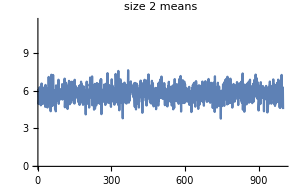
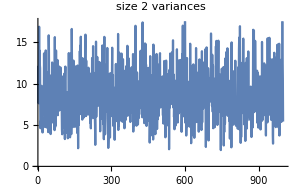
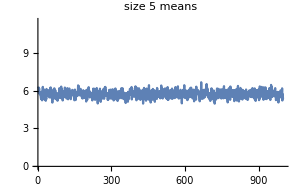
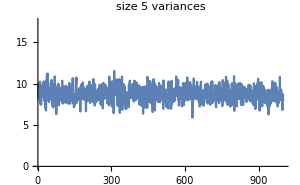
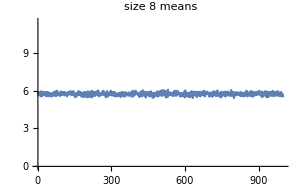
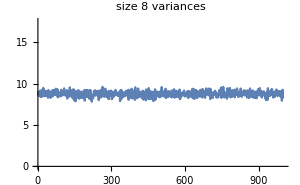
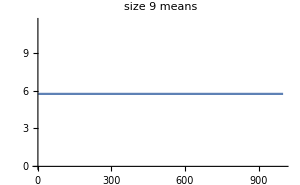
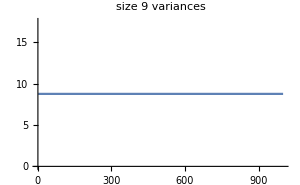

```mathematica
Table[func1[data1,sampleSize],{sampleSize,{2,5,8,9}}]
```

A média e variância entre n amostras variam de forma inversamente proporcional ao tamanho da amostra.

Agora, variar a quantidade de amostras tomadas.

```mathematica
Clear[func2];
func2=Function[{set,sampleCount},Module[{stats,statsTr,rs,mean,var},
	stats=Table[
		rs=Table[RandomSample[set,2],sampleCount];
			{Mean[Mean/@rs],
			Mean[Variance/@rs]}
	,1000];
	statsTr=Transpose[stats];
	{ListLinePlot[statsTr//First,ImageSize->300,PlotRange->{0,Mean[set]*2},
		PlotLabel->"count "<>ToString[sampleCount]<>" means"],
	ListLinePlot[statsTr//Last,ImageSize->300,PlotRange->{0,Variance[set]*2},
		PlotLabel->"count "<>ToString[sampleCount]<>" variances"]}
]];
```

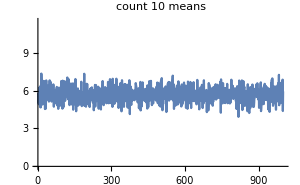
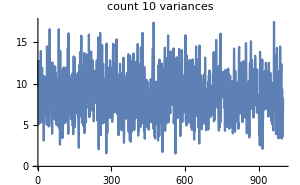
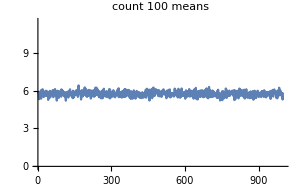
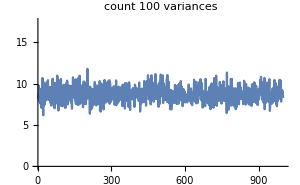
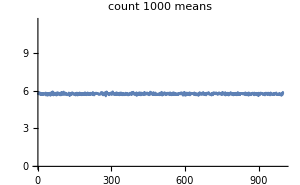
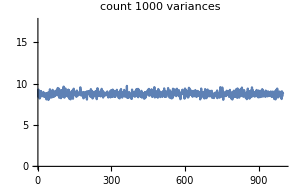
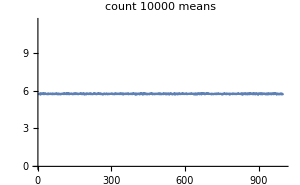
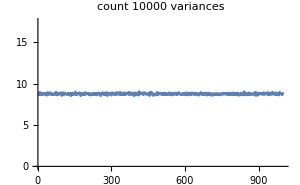

```mathematica
{func2[data1,10],func2[data1,100],func2[data1,1000],func2[data1,10000]}
```

Mesma coisa com a quantidade de amostras.

Mas ainda não respondi à minha questão. Porque a questão é que com todas as amostras, a estatística se iguala ao parâmetro, e eu quero ver as diferenças com menos que todas as amostras. Só que aqui, não são amostras randômicas... quer dizer, são, enquanto não são todas as amostras... Mas não é também uma questão de repetição do experimento. É uma questão combinatória.
Porque se não tomamos todas as amostras, tomamos uma parte possível de todas as amostras, e para cada número de amostras que deixamos de fora, há um número exato n de partes que seriam possíveis tomar sem estas amostras.

Alguns itens.

A diferença entre RandomSample e RandomSubsets é se as amostras podem repetir ou não. Basicamente, seria essa a diferença entre amostragem (infinita, com repetições de amostras, e de elementos, se com reposição) e tomada de subconjuntos (finita, sem repetições de amostras nem elementos, apenas a definição de se ordenação importa)?

Amostragem com/sem reposição ⟶ permutações e combinações, respectivamente? Não. Amostra com reposição significa mais de uma repetição de um elemento em uma amostra.

Sobre a diferença entre amostras e subconjuntos... subconjuntos são em número finito. A cada subconjunto que deixo de amostrar, há um resultado possível a mais de uma variável aleatória não representado nas amostras tomadas.

Morettin p. 26.

```mathematica
Clear[setm]
setm={1,2,3,4,5};
```

```mathematica
Table[RandomSample[setm,2],20]
```

{{3,4},{1,4},{5,1},{3,4},{1,4},{2,5},{2,5},{3,5},{4,5},{2,5},{2,1},{2,5},{5,2},{4,2},{4,2},{1,2},{2,1},{3,1},{2,1},{3,2}}

```mathematica
Subsets[setm,{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}}

```mathematica
Permutations[setm,{2}]
```

{{1,2},{1,3},{1,4},{1,5},{2,1},{2,3},{2,4},{2,5},{3,1},{3,2},{3,4},{3,5},{4,1},{4,2},{4,3},{4,5},{5,1},{5,2},{5,3},{5,4}}

```mathematica
Tuples[setm,2]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

São tuplas: subconjuntos ou amostras com reposição.
Sem reposição são permutações.
Permutações e tuplas são subconjuntos, mas com repetições.
Subconjuntos únicos não são utilizados.

Keeping, p. 12:

Theorem 1.9. The number of ordered arrangements (permutations) of n distinguishable objects is 1·2·...·n. This number is denoted by n! (read “factorial n”).
Theorem 1.10. The number of ways of selecting and arranging in order r out of n distinguishable objects is (n!)/((n-r)!). This is often denoted by (n)_r. When r=n, the result should reduce to n!, so that we must agree to define 0! as 1.

Theorem 1.11. The number of ways of arranging in order n_1 objects all alike of one kind, n_2 all alike of a second kind, and so on, up to k kinds of objects, is (n!)/(n_1! n_2! ...  n_k!), where ∑n_i=n.

Theorem 1.12. The number of ways of picking r out of n distinguishable objects, regargless of the order in which they are arranged, is called the number of combinations. It is given by (n
r)=(n!)/(r!(n-r)!)=((n)_r)/(r!). The symbol (n
r) may be read “n above r”. From the definition if follows immediately that (n
0)=(n
n). The symbol (n
r) for r>n is defined as 0.

Theorem 1.13. The binomial theorem for a positive integral index may be written 
(1+x)^n=
1+n x+(n(n-1))/(2!)x^2+...+x^n=
∑_(r=0)^n (n
r)x^r=
∑_(r=0)^∞ (n
r)x^r,
since all the coefficients (n
r) vanish when r>n.

```mathematica
Table[Print[sampleSize->N@{Mean[setm],Mean[Mean/@Tuples[setm,sampleSize]],Mean[Mean/@Permutations[setm,{sampleSize}]],Mean[Mean/@Subsets[setm,{sampleSize}]]}],{sampleSize,1,Length@setm}];
```

1→{3.,3.,3.,3.}

2→{3.,3.,3.,3.}

3→{3.,3.,3.,3.}

4→{3.,3.,3.,3.}

5→{3.,3.,3.,3.}

```mathematica
Table[Print[sampleSize->N@{Variance[setm],Mean[Variance/@Tuples[setm,sampleSize]],Mean[Variance/@Permutations[setm,{sampleSize}]],Mean[Variance/@Subsets[setm,{sampleSize}]]}],{sampleSize,2,Length@setm}];
```

2→{2.5,2.,2.5,2.5}

3→{2.5,2.,2.5,2.5}

4→{2.5,2.,2.5,2.5}

5→{2.5,2.,2.5,2.5}

Variância com apenas um elemento não existe.
Este é a média da variância amostral, a ilustração é a variância da média amostral.

```mathematica
Table[Print[sampleSize->N@{Variance[Mean/@Tuples[setm,sampleSize]],Variance[Mean/@Permutations[setm,{sampleSize}]],Variance[Mean/@Subsets[setm,{sampleSize}]]}],{sampleSize,1,Length@setm-1}];
```

1→{2.5,2.5,2.5}

2→{1.04167,0.789474,0.833333}

3→{0.672043,0.338983,0.37037}

4→{0.500801,0.12605,0.15625}

Subconjunto com todos os elementos é o próprio conjunto, apenas um elemento não tem variância. Já vimos que esta estatística resulta diferente. Sem subconjuntos:

```mathematica
Table[Print[sampleSize->N@{Variance[setm],Variance[Mean/@Tuples[setm,sampleSize]],Variance[Mean/@Permutations[setm,{sampleSize}]]}],{sampleSize,1,Length@setm}];
```

1→{2.5,2.5,2.5}

2→{2.5,1.04167,0.789474}

3→{2.5,0.672043,0.338983}

4→{2.5,0.500801,0.12605}

5→{2.5,0.400128,0.}

Do que concluímos que apesar das médias de todas as amostras com ou sem reposição de qualquer tamanho serem iguais, e portanto sua expectativa/média, a variância da média diminui progressivamente com o aumento do tamanho das amostras (até chegar a zero no conjunto total das amostras com reposição com tamanho igual ao da população).

As tuplas e permutações de amostras de tamanho 1 são iguais. Por isso as médias são iguais.

```mathematica
Tuples[setm,{1}]
```

{{1},{2},{3},{4},{5}}

```mathematica
Mean/@Tuples[setm,{1}]
```

{1,2,3,4,5}

```mathematica
Permutations[setm,{1}]
```

{{1},{2},{3},{4},{5}}

```mathematica
Mean/@Permutations[setm,{1}]
```

{1,2,3,4,5}

E as variâncias são iguais.

A variância das médias das permutações (= sem reposição) com o tamanho da amostra igual ao da população é zero.
Isso faz sentido porque nenhuma permutação de amostra de tamanho igual à população tem elemento faltando ou repetido que a população; são apenas todas as reordenações da população, conservando as médias.

```mathematica
Tuples[setm,{Length[setm]}]
```

{{1,1,1,1,1},{1,1,1,1,2},{1,1,1,1,3},{1,1,1,1,4},{1,1,1,1,5},{1,1,1,2,1},{1,1,1,2,2},{1,1,1,2,3},{1,1,1,2,4},{1,1,1,2,5},{1,1,1,3,1},{1,1,1,3,2},{1,1,1,3,3},{1,1,1,3,4},{1,1,1,3,5},{1,1,1,4,1},{1,1,1,4,2},3091,{5,5,5,2,4},{5,5,5,2,5},{5,5,5,3,1},{5,5,5,3,2},{5,5,5,3,3},{5,5,5,3,4},{5,5,5,3,5},{5,5,5,4,1},{5,5,5,4,2},{5,5,5,4,3},{5,5,5,4,4},{5,5,5,4,5},{5,5,5,5,1},{5,5,5,5,2},{5,5,5,5,3},{5,5,5,5,4},{5,5,5,5,5}}
 |  |  |  |

```mathematica
Permutations[setm,{Length[setm]}]
```

{{1,2,3,4,5},{1,2,3,5,4},{1,2,4,3,5},{1,2,4,5,3},{1,2,5,3,4},{1,2,5,4,3},{1,3,2,4,5},{1,3,2,5,4},{1,3,4,2,5},{1,3,4,5,2},{1,3,5,2,4},{1,3,5,4,2},{1,4,2,3,5},{1,4,2,5,3},{1,4,3,2,5},{1,4,3,5,2},{1,4,5,2,3},{1,4,5,3,2},{1,5,2,3,4},{1,5,2,4,3},{1,5,3,2,4},{1,5,3,4,2},{1,5,4,2,3},{1,5,4,3,2},{2,1,3,4,5},{2,1,3,5,4},{2,1,4,3,5},{2,1,4,5,3},{2,1,5,3,4},{2,1,5,4,3},{2,3,1,4,5},{2,3,1,5,4},{2,3,4,1,5},{2,3,4,5,1},{2,3,5,1,4},{2,3,5,4,1},{2,4,1,3,5},{2,4,1,5,3},{2,4,3,1,5},{2,4,3,5,1},{2,4,5,1,3},{2,4,5,3,1},{2,5,1,3,4},{2,5,1,4,3},{2,5,3,1,4},{2,5,3,4,1},{2,5,4,1,3},{2,5,4,3,1},{3,1,2,4,5},{3,1,2,5,4},{3,1,4,2,5},{3,1,4,5,2},{3,1,5,2,4},{3,1,5,4,2},{3,2,1,4,5},{3,2,1,5,4},{3,2,4,1,5},{3,2,4,5,1},{3,2,5,1,4},{3,2,5,4,1},{3,4,1,2,5},{3,4,1,5,2},{3,4,2,1,5},{3,4,2,5,1},{3,4,5,1,2},{3,4,5,2,1},{3,5,1,2,4},{3,5,1,4,2},{3,5,2,1,4},{3,5,2,4,1},{3,5,4,1,2},{3,5,4,2,1},{4,1,2,3,5},{4,1,2,5,3},{4,1,3,2,5},{4,1,3,5,2},{4,1,5,2,3},{4,1,5,3,2},{4,2,1,3,5},{4,2,1,5,3},{4,2,3,1,5},{4,2,3,5,1},{4,2,5,1,3},{4,2,5,3,1},{4,3,1,2,5},{4,3,1,5,2},{4,3,2,1,5},{4,3,2,5,1},{4,3,5,1,2},{4,3,5,2,1},{4,5,1,2,3},{4,5,1,3,2},{4,5,2,1,3},{4,5,2,3,1},{4,5,3,1,2},{4,5,3,2,1},{5,1,2,3,4},{5,1,2,4,3},{5,1,3,2,4},{5,1,3,4,2},{5,1,4,2,3},{5,1,4,3,2},{5,2,1,3,4},{5,2,1,4,3},{5,2,3,1,4},{5,2,3,4,1},{5,2,4,1,3},{5,2,4,3,1},{5,3,1,2,4},{5,3,1,4,2},{5,3,2,1,4},{5,3,2,4,1},{5,3,4,1,2},{5,3,4,2,1},{5,4,1,2,3},{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1},{5,4,3,1,2},{5,4,3,2,1}}

Ou seja, se retirarmos todas as amostras, com ou sem reposição, de qualquer tamanho, de uma população, a média das médias das amostras será igual à da população.

```mathematica
Mean/@Permutations[setm,{1}]
Mean[%]
```

{1,2,3,4,5}

3

```mathematica
N[Mean/@Permutations[setm,{2}]]
Mean[%]
```

{1.5,2.,2.5,3.,1.5,2.5,3.,3.5,2.,2.5,3.5,4.,2.5,3.,3.5,4.5,3.,3.5,4.,4.5}

3.

```mathematica
N[Mean/@Permutations[setm,{3}]]
Mean[%]
```

{2.,2.33333,2.66667,2.,2.66667,3.,2.33333,2.66667,3.33333,2.66667,3.,3.33333,2.,2.33333,2.66667,2.,3.,3.33333,2.33333,3.,3.66667,2.66667,3.33333,3.66667,2.,2.66667,3.,2.,3.,3.33333,2.66667,3.,4.,3.,3.33333,4.,2.33333,2.66667,3.33333,2.33333,3.,3.66667,2.66667,3.,4.,3.33333,3.66667,4.,2.66667,3.,3.33333,2.66667,3.33333,3.66667,3.,3.33333,4.,3.33333,3.66667,4.}

3.

```mathematica
N[Mean/@Permutations[setm,{4}]]
Mean[%]
```

{2.5,2.75,2.5,3.,2.75,3.,2.5,2.75,2.5,3.25,2.75,3.25,2.5,3.,2.5,3.25,3.,3.25,2.75,3.,2.75,3.25,3.,3.25,2.5,2.75,2.5,3.,2.75,3.,2.5,2.75,2.5,3.5,2.75,3.5,2.5,3.,2.5,3.5,3.,3.5,2.75,3.,2.75,3.5,3.,3.5,2.5,2.75,2.5,3.25,2.75,3.25,2.5,2.75,2.5,3.5,2.75,3.5,2.5,3.25,2.5,3.5,3.25,3.5,2.75,3.25,2.75,3.5,3.25,3.5,2.5,3.,2.5,3.25,3.,3.25,2.5,3.,2.5,3.5,3.,3.5,2.5,3.25,2.5,3.5,3.25,3.5,3.,3.25,3.,3.5,3.25,3.5,2.75,3.,2.75,3.25,3.,3.25,2.75,3.,2.75,3.5,3.,3.5,2.75,3.25,2.75,3.5,3.25,3.5,3.,3.25,3.,3.5,3.25,3.5}

3.

```mathematica
N[Mean/@Permutations[setm,{5}]]
Mean[%]
```

{3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.,3.}

3.

Caso especial, quando o tamanho das amostras é igual à população, obviamente as médias cada amostra são iguais à da população.

Agora vamos tirar algumas menos que todas amostras.

Vamos tirar RandomSamples anyway porque não haveria problema repetir amostra. Precisamos da aleatoriedade de escolha.

Como não são todas amostras, pode ser qualquer número arbitrário de amostras.

```mathematica
Module[{means},Table[
means=Mean/@Table[RandomSample[setm,3],20];
Print[N[means]];
Print[N[Mean[means]]];
,5];]
```

{3.66667,4.,3.66667,3.33333,4.,2.,2.66667,2.,2.33333,3.33333,3.,3.,3.66667,3.66667,4.,3.,3.,3.,2.66667,3.}

3.15

{3.,3.33333,3.33333,3.66667,3.,2.66667,2.66667,4.,2.,2.66667,2.33333,2.66667,2.,2.66667,2.66667,2.,3.,3.66667,2.,3.}

2.81667

{2.33333,2.66667,3.33333,4.,3.33333,3.,2.66667,2.66667,3.33333,3.33333,4.,3.,3.33333,2.33333,2.66667,2.66667,2.33333,3.33333,3.33333,3.}

3.03333

{3.,2.66667,3.,4.,2.66667,2.33333,3.33333,2.33333,3.33333,3.33333,2.,2.,2.,2.33333,3.,2.66667,4.,2.,3.,3.}

2.8

{4.,2.66667,3.,3.33333,2.33333,2.66667,3.,2.66667,4.,3.33333,2.66667,3.66667,3.33333,3.66667,3.33333,4.,3.33333,2.33333,3.,3.33333}

3.18333

Diferentes sample sizes.

```mathematica
Module[{means},Table[
means=Mean/@Table[RandomSample[setm,sampleSize],20];
N[Mean[means]],{sampleSize,1,Length[setm]}]]
```

{2.9,2.825,2.91667,2.9125,3.}

Examinar a variância destes resultados.

```mathematica
Table[RandomSample[setm,Length[setm]],20]
N[Mean[%]]
```

{{3,4,2,1,5},{4,1,3,5,2},{4,3,2,5,1},{2,4,1,3,5},{1,3,4,5,2},{4,5,3,2,1},{2,5,4,1,3},{4,2,1,3,5},{2,3,1,4,5},{1,5,4,2,3},{1,5,3,2,4},{1,4,5,2,3},{3,4,5,1,2},{2,3,5,1,4},{5,3,4,1,2},{3,4,1,5,2},{4,1,3,5,2},{2,3,4,5,1},{5,4,3,1,2},{5,4,2,3,1}}

{2.9,3.5,3.,2.85,2.75}

As amostras com tamanho igual à população incluem toda a população porque RandomSample é amostragem sem reposição. Então as médias ficam igual à população.

Proporção da variância da média da amostra com a variância da população.

```mathematica
Variance[setm]/Length[setm]
```

1/2

Conceito de distribuição. Não apenas o agrupamento e soma dos valores. A ordenação no eixo x e o “empilhamento” no eixo y, o que corresponde ao agrupamento e soma. E a soma não é dos valores, é da probabilidade. É a contagem manual da probabilidade por quantas vezes um valor ocorre em um conjunto.

```mathematica
{data1,Sort[data1]}
```

{{5,9,2,8.8,6.3,10.1,3.4,2.9,4.1},{2,2.9,3.4,4.1,5,6.3,8.8,9,10.1}}

```mathematica
Tally[log["PIM"][[1;;50]]]
```

{{4054,1},{0,1},{237,1},{2009,1},{4001,1},{4019,1},{6368,1},{10670,1},{6340,1},{1816,1},{3044,1},{2668,1},{3152,1},{908,1},{1497,1},{3205,1},{3250,1},{673,1},{4070,1},{3427,1},{4040,1},{1593,1},{1831,1},{2399,1},{515,1},{1603,1},{821,1},{478,1},{743,1},{637,1},{535,1},{461,1},{7732,1},{1786,1},{6008,1},{5172,1},{3545,1},{4404,1},{3477,1},{72,1},{351,1},{716,1},{1242,1},{4310,1},{10364,1},{7616,1},{10392,1},{8240,1},{11611,1},{11297,1}}

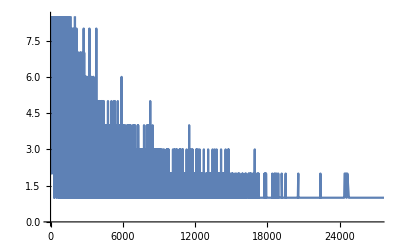

```mathematica
ListLinePlot[Sort[Tally[log["PIM"]]]]
```

Isto é uma distribuição.
A única coisa é que o histograma agrupa em bins.

```mathematica
Clear[log17855]
log17855=SemanticImport[
	NotebookDirectory[]<>"Log17855.csv",
	<|"PIM"->Automatic|>,
	"NamedColumns",HeaderLines->1,Delimiters->"\t"];
```

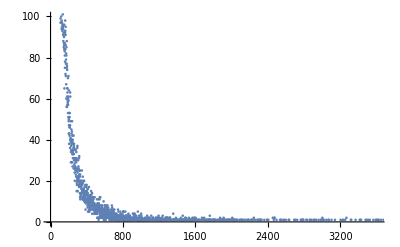

```mathematica
ListPlot[Tally[log17855["PIM"]],PlotRange->{0,100}]
```

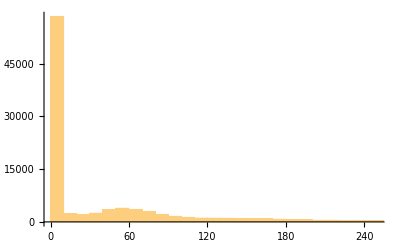

```mathematica
Histogram[log17855["PIM"],PlotRange->Automatic]
```

```mathematica
BinLists[log17855["PIM"],1000]
```

{{},8,{8309,8079}}
 |  |  |  |

```mathematica
Length[log17855["PIM"]]
```

99860

```mathematica
Downsample[log17855["PIM"],1000]
```

{702,256,396,504,0,0,48,0,96,9,66,129,119,116,231,519,0,92,0,17,78,44,0,41,323,72,3,4,12,0,0,19,0,0,425,77,31,0,13,0,45,0,77,85,26,62,156,27,138,0,3,98,0,224,0,42,3,30,45,0,0,116,0,48,9,152,41,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,745,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

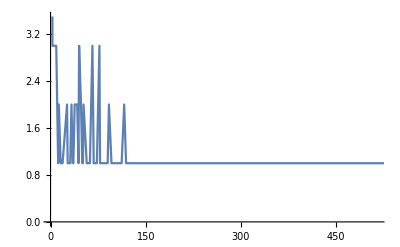

```mathematica
ListLinePlot[Sort[Tally[Downsample[log17855["PIM"],500]]]]
```

p. 26: As amostras (com reposição) são:

```mathematica
Tuples[setm,{2}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

As médias são:

```mathematica
DeleteDuplicates[N[Mean/@Tuples[setm,{2}]]]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.}

As frequências são:

```mathematica
Counts[N[Mean/@Tuples[setm,{2}]]]
```

<|1.→1,1.5→2,2.→3,2.5→4,3.→5,3.5→4,4.→3,4.5→2,5.→1|>

As probabilidades são (frequência ÷ contagem):

```mathematica
Clear[randVarDistr]
randVarDistr=Function[{set,rvar,dbg},Module[{samples,varvalues,counts},
	(*obter os valores da variável randômica para "todas as amostras com 
	reposição" = permutações, de um tamanho*)
	samples=Tuples[set,{2}];
	If[dbg,Print[samples]];
	varvalues=N[rvar/@samples];
	If[dbg,Print[varvalues]];
	(*agrupar contando (frequência)*)
	counts=Counts[varvalues];
	If[dbg,Print[counts]];
	(*dividir as frequências pela quantidade de amostras*)
	Association[Function[{key},key->counts[key]/Length[varvalues]]
		/@Keys[counts]]
]];
```

```mathematica
randVarDistr[setm,Mean,False]
```

<|1.→1/25,1.5→2/25,2.→3/25,2.5→4/25,3.→1/5,3.5→4/25,4.→3/25,4.5→2/25,5.→1/25|>

A distribuição é o conjunto completo de probabilidades. Ou seja, o conjunto completo de valores da variável randômica e suas probabilidades que somam a probabilidade 1.

As expectativas são (valor × probabilidade):

```mathematica
Clear[randVarExpect]
randVarExpect=Function[{set,rvar},Module[{distr,values},
	(*obter a distribuição*)
	distr=randVarDistr[set,rvar,False];
	(*multiplicar as probabilidades pelos valores*)
	(*os valores são as próprias chaves da associação*)
	Association[Function[{key},key->key*distr[key]]
		/@Keys[distr]]
]];
```

```mathematica
randVarExpect[setm,Mean]
```

<|1.→0.04,1.5→0.12,2.→0.24,2.5→0.4,3.→0.6,3.5→0.56,4.→0.48,4.5→0.36,5.→0.2|>

```mathematica
N@{1/25,3/25,6/25,10/25,15/25,14/25,12/25,9/25,5/25}
```

{0.04,0.12,0.24,0.4,0.6,0.56,0.48,0.36,0.2}

(x̄)^2·P(x̄): (Não acho que isso é variância)

```mathematica
Clear[randVarSq]
randVarSq=Function[{set,rvar},Module[{distr,values},
	(*obter a distribuição*)
	distr=randVarDistr[set,rvar,False];
	(*multiplicar as probabilidades pelos valores ao quadrado*)
	(*os valores são as próprias chaves da associação*)
	Association[Function[{key},key->key^2*distr[key]]
		/@Keys[distr]]
]];
```

```mathematica
randVarSq[setm,Mean]
```

<|1.→0.04,1.5→0.18,2.→0.48,2.5→1.,3.→1.8,3.5→1.96,4.→1.92,4.5→1.62,5.→1.|>

```mathematica
N@{1/25,4.5/25,12/25,25/25,45/25,49/25,48/25,40.5/25,25/25}
```

{0.04,0.18,0.48,1.,1.8,1.96,1.92,1.62,1.}

Obter um “histograma” das probabilidades.

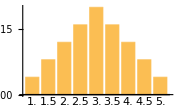

```mathematica
Module[{distr},distr=randVarDistr[setm,Mean,False];
BarChart[distr,ChartLabels->Keys[distr],ImageSize->Small]]
```

```mathematica
(*HistogramList[setm]*)
```

{{0,2,4,6},{1,2,2}}

Estas são as probabilidades da média (valor da variável randômica) ser algum destes em uma determinada amostra.

É normal.
Agora podemos fazer isto para qualquer conjunto e variável.

{{1,1},{1,2},{1,3},{1,4},{1,5},{2,1},{2,2},{2,3},{2,4},{2,5},{3,1},{3,2},{3,3},{3,4},{3,5},{4,1},{4,2},{4,3},{4,4},{4,5},{5,1},{5,2},{5,3},{5,4},{5,5}}

{0.,0.5,2.,4.5,8.,0.5,0.,0.5,2.,4.5,2.,0.5,0.,0.5,2.,4.5,2.,0.5,0.,0.5,8.,4.5,2.,0.5,0.}

<|0.→5,0.5→8,2.→6,4.5→4,8.→2|>

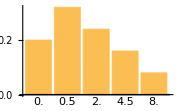

```mathematica
Module[{distr},distr=randVarDistr[setm,Variance,True];
BarChart[distr,ChartLabels->Keys[distr],ImageSize->Small]]
```

Idem para a variância ser esta em uma determinada amostra.

Porém, não estamos calculando as expectativas das variáveis randômicas.
Apenas a distribuição de probabilidades do valor da variável randômica em uma amostra qualquer.
A questão é se é isto em que é avaliada a distribuição na teoria:
“A média das médias amostrais é igual à média populacional.”
A média das médias amostrais é a esperança, ou seja, um passo depois da probabilidade.
A “variância da média amostral” (agora já não mais no plural) já nem é mais a esperança.
Mas o importante é que, em ambos os casos, não se trata mais de distribuições.

Mas p. 28: “A distribuição da variável x̄ (...) será sempre normal com a mesma média da população e variância n vezes menor.” e p. 29: “se a população X não é normal, a variável x̄ não será “exatamente” normal, mas sim aproximadamente normal, tendo como distribuição limite a distribuição N(0,1).”. (O que é esta distribuição?)

### Relação entre experimento e população

Exemplos de experimentos.
Definido um experimento (exemplo: uma rolagem de um dado de 6 faces), o espaço amostral são todos os pontos amostrais possíveis: {1,2,3,4,5,6}.

3 rolagens de um dado de 6 faces: {{1,1,1},{1,1,2},...,{6,6,6}}.

E aqui temos: são todas as combinações. Combinações de que?

3 rolagens/experimentos quer dizer vamos tirar 3 amostras randômicas de uma população.

Os possíveis resultados ({1,2,3,4,5,6}) são a população.

Da qual estamos tirando 3 amostras, com reposição: as “amostras” são independentes.

O resultado de cada amostra ou repetição do experimento forma um ponto amostral: {1,3,5} e {2,4,6}, por exemplo.

Estou considerando experimento como a unidade e “repetições de um experimento” um multiplicador. Mas está errado; o experimento inteiro é a repetição. Então o experimento são as 3 rolagens.

Agora sim, cada resultado do experimento completo forma um ponto amostral: {1,3,5} e {2,4,6}, por exemplo.

Não consideramos as subdivisões ou “subexperimentos”, por não ser útil.

O conjunto de todas as combinações dos pontos amostrais forma o espaço amostral.

```mathematica
Take[Tuples[{1,2,3,4,5,6},{3}],20]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,4,1},{1,4,2}}

Novamente, a quantidade de “subexperimentos” indica o tamanho dos pontos amostrais, mas não é interessante formalizar isto.

Eventos são subconjuntos do espaço amostral. O que quer dizer que podem conter n pontos amostrais.
Eventos são “quais pontos amostrais são considerados como um resultado x, ou um resultado y”. Isso significa que eventos são agrupamentos de pontos amostrais.

#### Paralelo com a estatística

Na estatística, tiramos n amostras de uma população.
No experimento, a quantidade de amostras determinou o tamanho do ponto amostral.
Na estatística é a mesma coisa: se formos tirar 3 amostras com reposição da população {1,2,3,4,5,6}, teremos pontos amostrais possíveis com 3 elementos (os mesmos tuples).

## 4 - Estimação

## 5 - Intervalos de confiança para médias e proporções

## 6 - Testes de hipóteses para médias e proporções

## 7 - Erros de decisão

## 8 - Distribuição de t de Student IC E TH para a média de população normal com variância desconhecida

## 9 - Comparação de duas médias: TH para a diferença de duas médias

## 10 - Distribuição de x^2 Qui-Quadrado IC e TH para a variância de populações normais

## 11 - Testes de aderência e tabelas de contingência

## 12 - Distribuição de F de Fisher-Snedecor IC e TH para quociente de variâncias

1	https://en.wikipedia.org/wiki/Expected_value

2	https://en.wikipedia.org/wiki/Weighted_arithmetic_mean

3	https://en.wikipedia.org/wiki/Expected_value

4	http://mathworld.wolfram.com/ExpectationValue.html

5	https://en.wikipedia.org/wiki/Sampling_(statistics)

6	https://en.wikipedia.org/wiki/Sample_(statistics)

7	https://en.wikipedia.org/wiki/Order_statistic

8	https://www.probabilitycourse.com/chapter2/2_1_1_ordered_with_replacement.php

9	https://en.wikipedia.org/wiki/Binomial_coefficient